InterpolatingFunction::dmval: Input value {39291.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

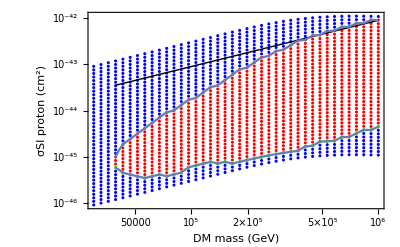

1600

```mathematica
xenontab={{67.1088847047298,6.491199097404529 10^-47},
{85.71364161700875,7.979226336320964 10^-47},
{112.7385029514892,1.0195378685327386 10^-46},
{160.3618125668259,1.407535586151586  10^-46},
{243.0859343070418,2.0860644934719864 10^-46},
{310.47723035488053,2.6654485756533687 10^-46},
{418.48419914039226,3.563040249104596 10^-46},
{553.1294474634739,4.732275586026907 10^-46},
{682.6827292375224,5.8547317673333095 10^-46},
{830.2996532165596,7.150587686439543 10^-46}};
xenontabfull={{6.098821205160766,2.0876343187969483 10^-44},{6.191605519036322,1.7982895113343166 10^-44},
{6.285801405511198,1.5185373767576632 10^-44},
{6.405564034332244,1.2951229972225534 10^-44},
{6.552295006843687,1.0405875312869496 10^-44},
{6.830086903328947,7.273962509069876 10^-45},
{7.119656098863208,5.0846785102179476 10^-45},
{7.4777422569957395,3.4156811406204636 10^-45},
{7.943282347242811,2.2050199697034544 10^-45},
{8.663730174238891,1.2384331546710343 10^-45},
{9.307916079466379,7.994803158635672 10^-46},
{9.99999999999999,5.478490427237894 10^-46},
{10.542675023868389,4.230092770328957 10^-46},
{11.28389448375254,3.0769536221260366 10^-46},
{12.260963234449527,2.1940812181475293 10^-46},
{13.627815006174735,1.503508305544695 10^-46},
{15.147043367743969,1.0936463046607286 10^-46},
{16.835635256301977,8.278021801961589 10^-47},
{18.712471312178835,6.520109052477533 10^-47},
{21.194809047856346,5.291053058335585 10^-47},
{24.463837886916085,4.557716422386298 10^-47},
{28.88389367953851,4.2091079563549744 10^-47},
{34.490931061051995,4.2091079563549744 10^-47},
{39.362435972277055,4.423727196396997 10^-47},
{43.91601763643997,4.695764016327442 10^-47},
{50.30826550447146,5.186839479118506 10^-47},
{58.06767349941279,5.78654062501237 10^-47},
{68.04353770075883,6.585284072066683 10^-47},
{77.36144803177547,7.3466730489097 10^-47},
{94.13919750179002,8.700111890077747 10^-47},
{109.48238818676117,1.0000000000000164 10^-46},
{130.24291219623336,1.1725043721826276 10^-46},
{154.94013656716123,1.3747665027873325 10^-46},
{180.19291249039173,1.5801710600472428 10^-46},
{224.29504119456442,1.9472281830260163 10^-46},
{279.1911446969589,2.3995488163525163 10^-46},
{347.52304314022973,2.9569387770009658 10^-46},
{432.57914087688965,3.71701560558461 10^-46},
{559.1662926205971,4.7663479705687954 10^-46},
{706.6108925191503,6.05142216158352 10^-46},
{879.5535687596032,7.606931460853561 10^-46}};

xenonint=Interpolation[xenontabfull,InterpolationOrder->1];
SetDirectory[NotebookDirectory[]];
(*tab=Import["eflux0old","TSV"]//ToExpression;
tab=Flatten[tab,1];
*)
tabsimp=Import["efluxSImA1.mx"]//ToExpression;
tabsimp=Flatten[tabsimp,1];
tab=Import["scanefluxmA1.mx"]//ToExpression;
isexcluded[table_]:=Table[If[table[[i,6,1]]/1000.>2.2 10^-12||table[[i,6,2]]/1000.>8.8 10^-13||table[[i,6,3]]/1000.>2.8 10^-13||table[[i,6,4]]/1000.>8.1 10^-14||table[[i,6,5]]/1000.>6.3 10^-14,1,0],{i,1,Length[tab]}]
exc=isexcluded[tab];
isexcludedsimp[table_]:=Table[If[table[[i,3,1]]/1.>2.2 10^-12||table[[i,3,2]]/1.>8.8 10^-13||table[[i,3,3]]/1.>2.8 10^-13||table[[i,3,4]]/1.>8.1 10^-14||table[[i,3,5]]/1.>6.3 10^-14,1,0],{i,1,Length[tabsimp]}]
excsimp=isexcludedsimp[tabsimp];
exctabsimp={};
allowedtabsimp={};
Do[If[excsimp[[i]]==1,exctabsimp=Append[exctabsimp,{tabsimp⟦i,1⟧,tabsimp⟦i,2⟧}]],{i,1,Length[tabsimp]}]
Do[If[excsimp[[i]]==0,allowedtabsimp=Append[allowedtabsimp,{tabsimp⟦i,1⟧,tabsimp⟦i,2⟧}]],{i,1,Length[tabsimp]}]
massessimp=DeleteDuplicates[Table[exctabsimp[[i,1]],{i,1,Length[exctabsimp]}]];
minxsectionssimp={};
maxxsectionssimp={};
Do[
particularmasssimp=Select[exctabsimp,#[[1]]==massessimp[[j]]&];
minxsectionssimp=Append[minxsectionssimp,Min[Table[particularmasssimp[[i,2]],{i,1,Length[particularmasssimp]}]]];
maxxsectionssimp=Append[maxxsectionssimp,Min[Table[particularmasssimp[[i,2]],{i,1,Length[particularmasssimp]}]]];
,{j,1,Length[massessimp]}]
minexcsimp=Table[{massessimp[[i]],minxsectionssimp[[i]]},{i,1,Length[massessimp]}];
minexcfuncsimp=Interpolation[minexcsimp,InterpolationOrder->1];
(*exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,4⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,4⟧}]],{i,1,Length[tab]}]
ListLogLogPlot[{exctab,allowedtab},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","ϵ"},PlotStyle->{Red,Blue}];*)
exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,7⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,7⟧}]],{i,1,Length[tab]}]
masses=DeleteDuplicates[Table[exctab[[i,1]],{i,1,Length[exctab]}]];
minxsections={};
maxxsections={};
Do[
particularmass=Select[exctab,#[[1]]==masses[[j]]&];
minxsections=Append[minxsections,Min[Table[particularmass[[i,2]],{i,1,Length[particularmass]}]]];
maxxsections=Append[maxxsections,Max[Table[particularmass[[i,2]],{i,1,Length[particularmass]}]]];,{j,1,Length[masses]}]
minexc=Table[{masses[[i]],minxsections[[i]]},{i,1,Length[masses]}];
minexcfunc=Interpolation[minexc,InterpolationOrder->1];
maxexc=Table[{masses[[i]],maxxsections[[i]]},{i,1,Length[masses]}];
maxexcfunc=Interpolation[maxexc,InterpolationOrder->1];
(*logLogRegionPlot[rplot_]:=Module[{pts,pgon},pts=Cases[Normal@rplot,Line[a__]:>a,Infinity];
pgon={EdgeForm[],Directive[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
ListLogLogPlot[pts,Joined->True,Frame->True,PlotRange->All,AspectRatio->1,Axes->False,PlotStyle->ColorData[1][1],Epilog->(pgon/.{x_,y_?NumericQ}:>Log@{x,y})]]
rplot=RegionPlot[σ<maxexcfunc[mdm]&&σ>minexcfunc[mdm],{mdm,Min[masses],Max[masses]},{σ,Min[minxsections],Max[maxxsections]},MaxRecursion->7,ColorFunction->"DarkRainbow"];*)
Show[ListLogLogPlot[{exctab,allowedtab,minexc},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"},PlotStyle->{Red,Blue,Green}],LogLogPlot[xenonint[x],{x,Min[masses],Max[masses]},PlotStyle-> {Thick,Black}],LogLogPlot[minexcfunc[mdm],{mdm,Min[masses],Max[masses]}],LogLogPlot[maxexcfunc[mdm],{mdm,Min[masses],Max[masses]}],PlotRange->All]
(*ContourPlot[intfunc[mχ,σ],{mχ,1000.,100000},{σ,10^-50,10^-40},Contours-> {{0.9}},ContourShading-> {White,Red},ScalingFunctions-> {"Log","Log"},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"}]*)
Length[tab]
exctab;
allowedtab;
```

```mathematica
$outputfolder="scanfiles";
SetDirectory[NotebookDirectory[]<>"/"<>$outputfolder];
filenames=FileNames[];
data={};
Do[data=Append[data,Import[filenames⟦i⟧]],{i,1,Length[filenames]}];
data=Flatten[data,2];
SetDirectory[NotebookDirectory[]];
Export["scanefluxmA1.mx",data];
```

```mathematica
1000 mm/c/.{c-> 3 10^8 m/s, mm-> 0.001 m}
```

3.33333×10^-9 s

```mathematica
logLogRegionPlot[rplot_]:=Module[{pts,pgon},pts=Cases[Normal@rplot,Line[a__]:>a,Infinity];
pgon={EdgeForm[],Directive[Red,AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
ListLogLogPlot[pts,Joined->True,Frame->True,PlotRange->All,AspectRatio->1,Axes->False,PlotStyle->Red(*ColorData[1][1]*),Epilog->(pgon/.{x_,y_?NumericQ}:>Log@{x,y})]]
```

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {35365.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

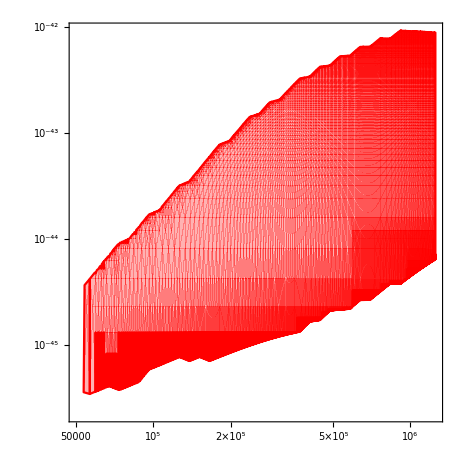

```mathematica
rplot=logLogRegionPlot@RegionPlot[σ<maxexcfunc[mdm]&&σ>minexcfunc[mdm],{mdm,0.9Min[masses],1.25Max[masses]},{σ,Min[minxsections],1.7Max[maxxsections]},PlotRange-> {{Min[masses],1.1Max[masses]},{Min[minxsections],xenonint[Max[massessimp]]}},WorkingPrecision-> 2,PlotPoints->200,MaxRecursion->4]
```

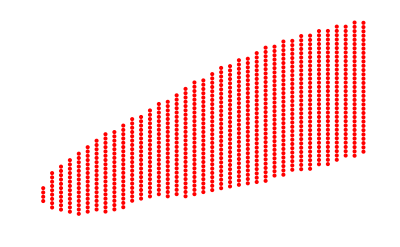

```mathematica
exclistplot=ListLogLogPlot[exctab,(*PlotRange-> {{Min[masses],1.1Max[masses]},{Min[minxsections],xenonint[Max[massessimp]]}},*)Axes->False,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"},PlotStyle->Red]
```

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

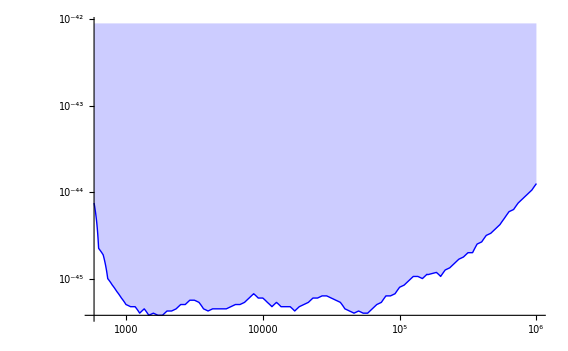

```mathematica
rplotsimp=LogLogPlot[minexcfuncsimp[mdm],{mdm,Min[massessimp],Max[massessimp]},PlotRange->{{Min[massessimp],Max[massessimp]},{Min[minxsectionssimp],xenonint[Max[massessimp]]}},Filling->Top,PlotStyle-> {Blue,Thick}]


(*logLogRegionPlot@RegionPlot[σ>minexcfuncsimp[mdm],{mdm,Min[massessimp],Max[massessimp]},{σ,Min[minxsectionssimp],xenonint[Max[massessimp]]},WorkingPrecision-> 1,PlotPoints->100,MaxRecursion->2]*)
```

```mathematica
xenonplot=LogLogPlot[xenonint[x],{x,1,10^6},PlotStyle-> {Thick,Black},Filling->Top];
```

InterpolatingFunction::dmval: Input value {1.00028} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

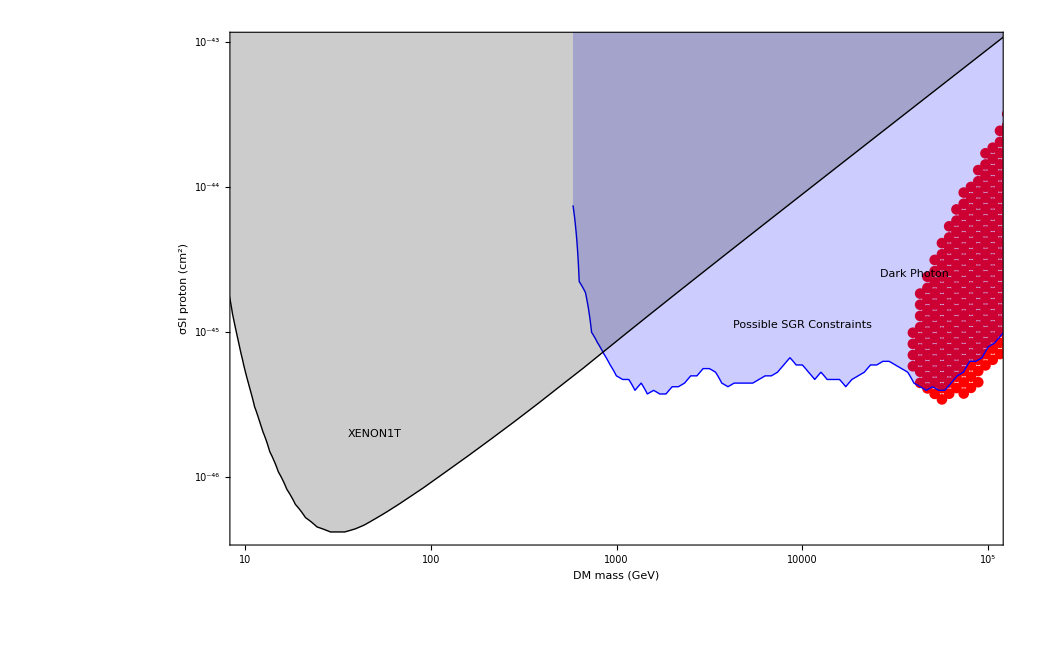

```mathematica
pgon={EdgeForm[],Directive[Red,AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
Show[exclistplot(*rplot*),rplotsimp,xenonplot,PlotRange-> {{Log[10.],Log[10.^5]},{Log[4 10.^-47],Log[10.^-43]}},Frame->True,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"},FrameStyle->Black,LabelStyle->25,Epilog-> {Style[Text["XENON1T",{Log[50],Log[2 10^-46]}],20],Style[Text["Possible SGR Constraints",{Log[10^4],Log[2 10^-45.25]}],20,Blue],Style[Text["Dark Photon",{Log[10^4.6],Log[10^-44.6]}],20,Red](*,pgon*)}]
```

```mathematica
tabsimp=Import["efluxSImA1.mx"]//ToExpression;
tabsimp=Flatten[tabsimp,1]
tabsimp=Import["efluxSImA5.mx"]//ToExpression;
tabsimp=Flatten[tabsimp,1]
```

{{500.,1.×10^-47,{0.,0.,0.,0.,0.}},{500.,1.05925×10^-47,{0.,0.,0.,0.,0.}},{500.,1.12202×10^-47,{0.,0.,0.,0.,0.}},12095,{1.×10^6,9.44061×10^-45,{1.99638×10^-13,9.64594×10^-13,6.26733×10^-12,4.77656×10^-11,2.81188×10^-10}},{1.×10^6,1.×10^-44,{2.11467×10^-13,1.02175×10^-12,6.63869×10^-12,5.05959×10^-11,2.9785×10^-10}}}
 |  |  |  |

{{500.,1.×10^-46,{0.,0.,0.,0.,0.}},{500.,1.05925×10^-46,{0.,0.,0.,0.,0.}},{500.,1.12202×10^-46,{0.,0.,0.,0.,0.}},12095,{1.×10^6,9.44061×10^-44,{6.18101×10^-15,1.9211×10^-14,5.91194×10^-14,1.82236×10^-13,4.77345×10^-13}},{1.×10^6,1.×10^-43,{6.54726×10^-15,2.03493×10^-14,6.26224×10^-14,1.93034×10^-13,5.05629×10^-13}}}
 |  |  |  |